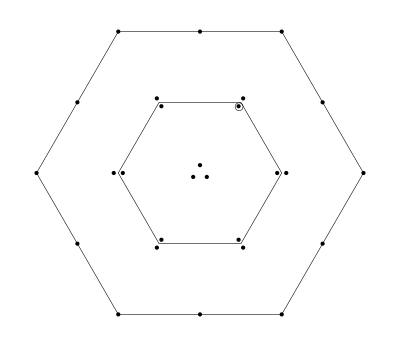

Y=1.5,  I_3=0.5

-4uu(ūs̄+s̄ū)+3(ud+du)(s̄d̄+d̄s̄)+(us+su)s̄s̄

```mathematica
(*-------------------------------*)
```

The current J:

3 (d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_a 1C((s̄)_b)^T)+3 (d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_b 1C((s̄)_a)^T)+3 (d_a^T C1 u_b+u_a^T C1 d_b) ((s̄)_a 1C((d̄)_b)^T)+3 (d_a^T C1 u_b+u_a^T C1 d_b) ((s̄)_b 1C((d̄)_a)^T)+((s̄)_a 1C((s̄)_b)^T) (s_a^T C1 u_b+u_a^T C1 s_b)+((s̄)_b 1C((s̄)_a)^T) (s_a^T C1 u_b+u_a^T C1 s_b)-4 (u_a^T C1 u_b) ((s̄)_a 1C((ū)_b)^T+(s̄)_b 1C((ū)_a)^T)-4 (u_a^T C1 u_b) ((ū)_a 1C((s̄)_b)^T+(ū)_b 1C((s̄)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
3 (d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 u)+3 (d̄(γ^μ).(γ̄)^5 u s̄(γ^μ).(γ̄)^5 d)+3 (d̄ γ^μ d s̄ γ^μ u)+3 (d̄ γ^μ u s̄ γ^μ d)+(4 (ū(γ̄)^5 u)-3 (d̄(γ̄)^5 d)) (s̄(γ̄)^5 u)-3 (d̄(γ̄)^5 u s̄(γ̄)^5 d)+3/2 (d̄ σ^μν d s̄ σ^μν u)+3/2 (d̄ σ^μν u s̄ σ^μν d)+(4 (ū 1u)-3 (d̄ 1d)) (s̄ 1u)-3 (d̄ 1u s̄ 1d)+s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 u-4 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 u)+s̄ γ^μ s s̄ γ^μ u-4 (s̄ γ^μ u ū γ^μ u)-s̄(γ̄)^5 s s̄(γ̄)^5 u+1/2 (s̄ σ^μν s s̄ σ^μν u)-2 (s̄ σ^μν u ū σ^μν u)-s̄ 1s s̄ 1u
```

Π(q^2)=
-(7 log(-q^2/μ^2) q^8)/(768 π^6)+(35 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(192 π^5)-(3 ⟨ d̄ d⟩ log(-q^2/μ^2) (m_d+m_s+m_u) q^4)/(2 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (36 m_d+41 m_s+34 m_u) q^4)/(24 π^4)-(⟨ ū u⟩ log(-q^2/μ^2) (36 m_d+34 m_s+131 m_u) q^4)/(24 π^4)-(6 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2+(175 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(1728 π^6)+(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2+(28 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(50 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(23 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(8 π^2)-(85 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(24 π^2)-(25 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(85 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(24 π^2)-(13 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(72 π^2)-(199 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(36 π^2)-(25 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(199 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(36 π^2)-(26 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)-(2 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(5 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(18 π q^2)-(40 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-(3 ⟨ d̄ Gd⟩^2)/(32 π^2 q^2)+(127 ⟨ s̄ Gs⟩^2)/(1152 π^2 q^2)+(127 ⟨ ū Gu⟩^2)/(72 π^2 q^2)-(7 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(3 π q^2)+(13 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(3 π q^2)+(5 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(6 π q^2)+(135 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(64 π^2 q^2)+(155 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(64 π^2 q^2)+(2459 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(1152 π^2 q^2)-(2 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (-8 m_d+4 m_s-8 m_u))/q^2+(64 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_s+m_u))/(3 q^2)-(16 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (m_s+2 m_u))/(3 q^2)-(2 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (-8 m_d-8 m_s+4 m_u))/q^2+(4 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (48 m_d+20 m_s+40 m_u))/(3 q^2)+(16 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (8 m_s+52 m_u))/(9 q^2)+(2 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (56 m_s+64 m_u))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

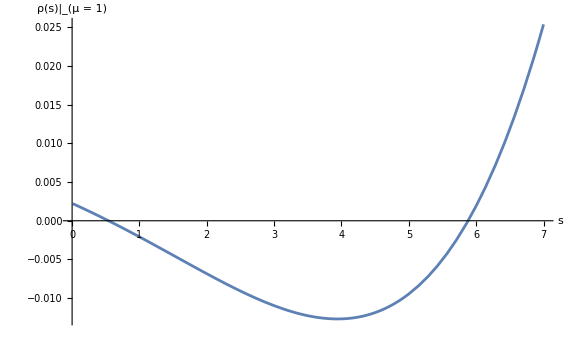
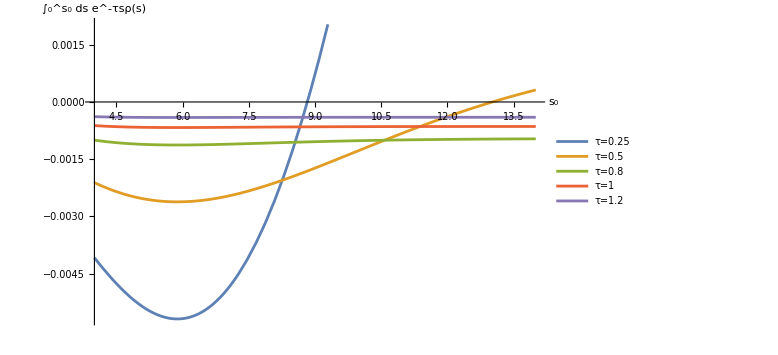

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

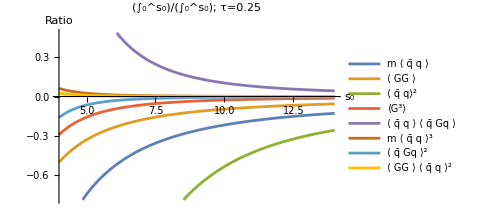
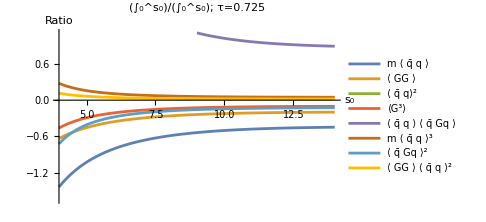
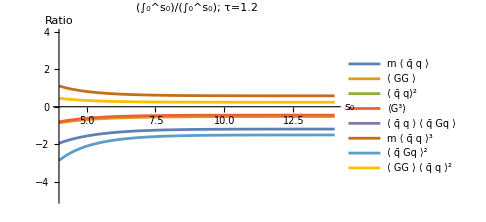

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

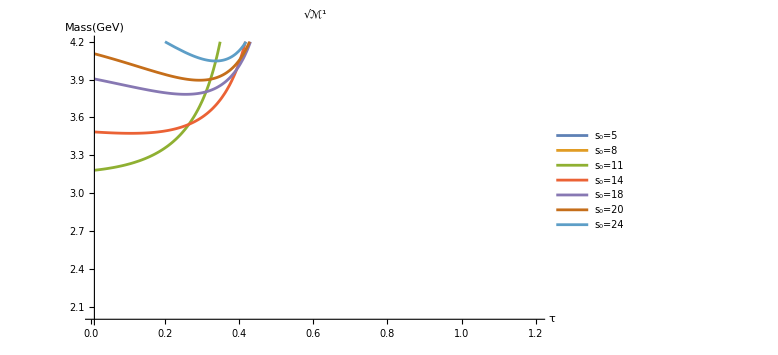
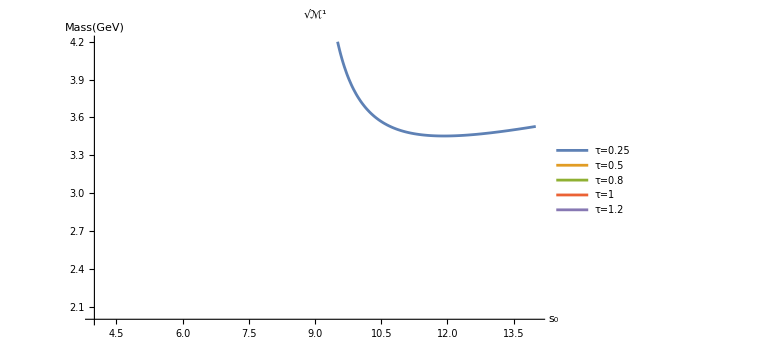

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

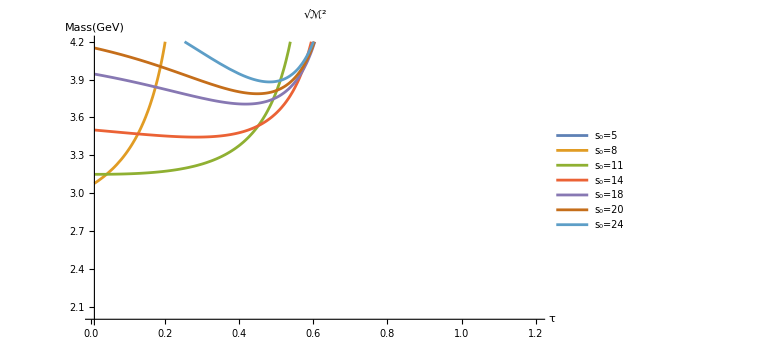
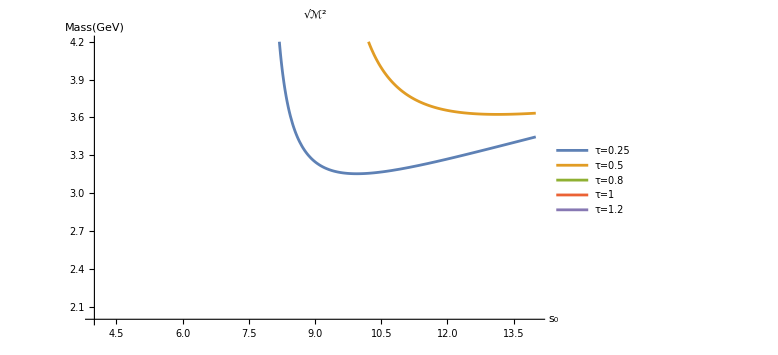

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

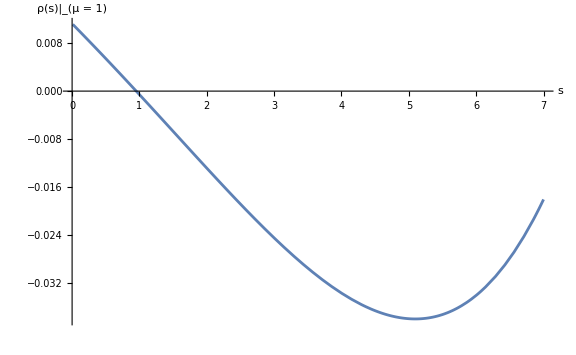
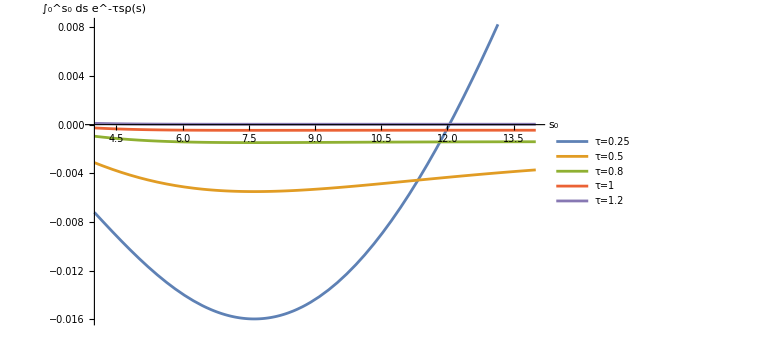

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

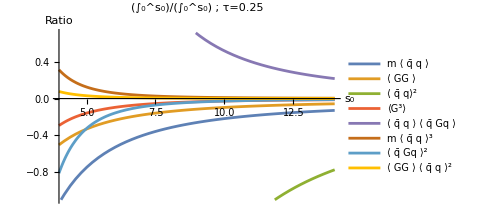
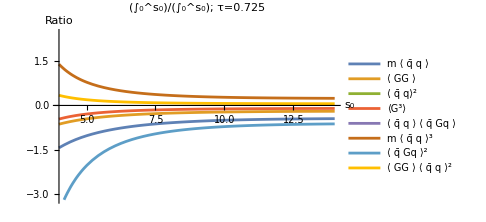
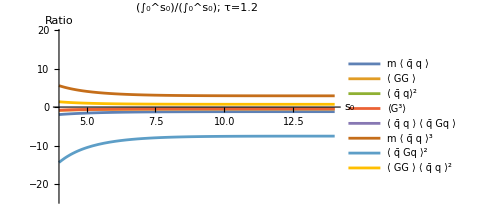

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

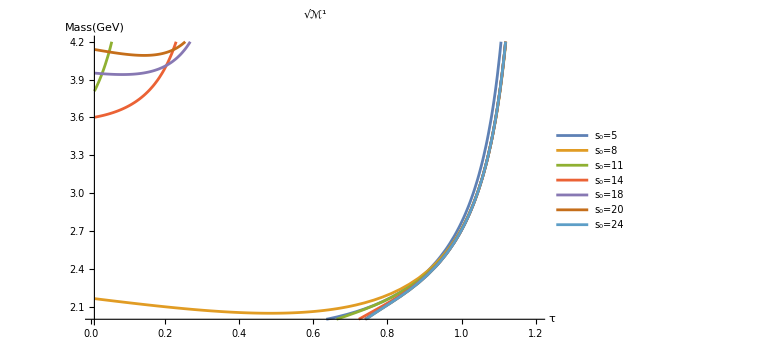
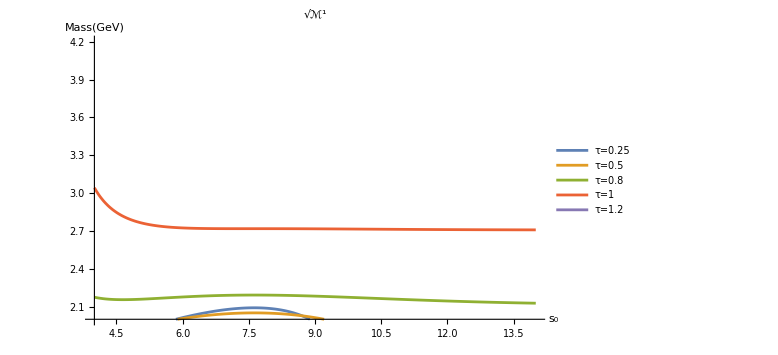

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5